#### Distribución Binomial

Función de probabilidad y función característica

```mathematica
PDF[BinomialDistribution[n,p],x]
```

Piecewise[{{(1-p)^(n-x) p^x Binomial[n,x], 0≤x≤n}, {0, True}}]

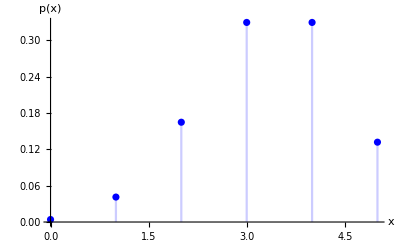

```mathematica
DiscretePlot[PDF[BinomialDistribution[5,2/3],x],{x,0,5.},PlotStyle->Blue,AxesLabel->{x,p[x]}]
```

Directamente

Comando: CharacteristicFunction

```mathematica
CharacteristicFunction[BinomialDistribution[n,p],t]
```

(1-p+ⅇ^(ⅈ t) p)^n

Mediante la Transformada de Fourier. Si quisiéramos usar la transformada de Fourier en el caso discreto habría que usar FourierSequenceTransform, con FourierParameters->{1,-1}, ya que la definición que usa Mathematica es
(|b/(2 π)|)^((1-a)/2)∑_(x=-∞)^∞ f(x) ⅇ^(-ⅈ b x t)

Comando: FourierSequenceTransform

Opciones: FourierParameters→{1,-1}

```mathematica
FourierSequenceTransform[PDF[BinomialDistribution[n,p],x],x,t,FourierParameters->{1,-1}]
```

Piecewise[{{(1+(-1+ⅇ^(ⅈ t)) p)^n, n≥0}, {0, True}}]

Mediante la esperanza

Comando: Expectation

```mathematica
Expectation[ⅇ^(ⅈ t XB),XB\[Distributed]BinomialDistribution[n,p]]
```

(1+(-1+ⅇ^(ⅈ t)) p)^n

Mediante la integral de Lebesgue (sumatorio)

Comando: Sum o con la paleta

```mathematica
Sum[ⅇ^(ⅈ t x)PDF[BinomialDistribution[n,p],x],{x,0,n}]
```

Piecewise[{{(1-p)^n, n==0}, {(1+(-1+ⅇ^(ⅈ t)) p)^n, True}}]

```mathematica
∑_(x=0)^n ⅇ^(ⅈ t x)PDF[BinomialDistribution[n,p],x]
```

Piecewise[{{(1-p)^n, n==0}, {(1+(-1+ⅇ^(ⅈ t)) p)^n, True}}]

```mathematica
Piecewise[{{(1-p)^n,n==0}},(1+(-1+ⅇ^(ⅈ t)) p)^n]
```

Piecewise[{{0, n==0}, {ⅈ ⅇ^(ⅈ t) n p (1+(-1+ⅇ^(ⅈ t)) p)^(-1+n), True}}]

```mathematica
Simplify[%8]
```

(1+(-1+ⅇ^(ⅈ t)) p)^n

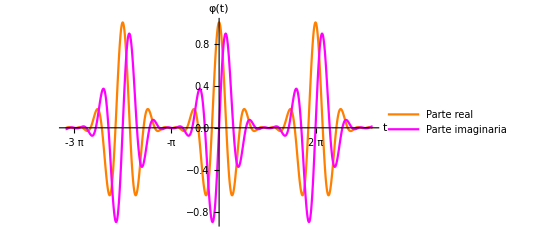

```mathematica
Plot[{Re[CharacteristicFunction[BinomialDistribution[5,2/3],t]],Im[CharacteristicFunction[BinomialDistribution[5,2/3],t]]},{t,-10,10},PlotStyle->{Orange,Magenta},AxesLabel->{t,φ[t]},PlotRange->Full,PlotLegends->{"Parte real","Parte imaginaria"},Ticks->{{-Pi,-2 Pi,-3Pi,Pi,2 Pi,3Pi},Automatic}]
```

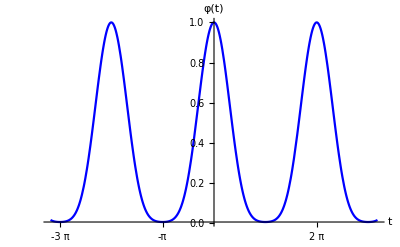

```mathematica
Plot[Abs[CharacteristicFunction[BinomialDistribution[5,2/3],t]],{t,-10,10},PlotStyle->Blue,AxesLabel->{t,φ[t]},PlotRange->Full,Ticks->{{-Pi,-2 Pi,-3Pi,Pi,2 Pi,3Pi},Automatic}]
```

```mathematica
ParametricPlot3D[{t,Re[CharacteristicFunction[BinomialDistribution[10,2/3],t]],Im[CharacteristicFunction[BinomialDistribution[10,2/3],t]]},{t,-20,20},BoxRatios->{1.5,1,1},PlotRange->{{-20,20},{-1,1},{-1,1}},PlotStyle->Red, AxesLabel->{t,Re[φ[t]],Im[φ[t]]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t,Re[CharacteristicFunction[BinomialDistribution[10,2/3],t]],Im[CharacteristicFunction[BinomialDistribution[10,2/3],t]]},{t,-2,2},BoxRatios->{1.5,1,1},PlotRange->{{-3,3},{-1,1},{-1,1}},PlotStyle->Blue, AxesLabel->{t,Re[φ[t]],Im[φ[t]]},ViewPoint->Right]
```

-Graphics3D-

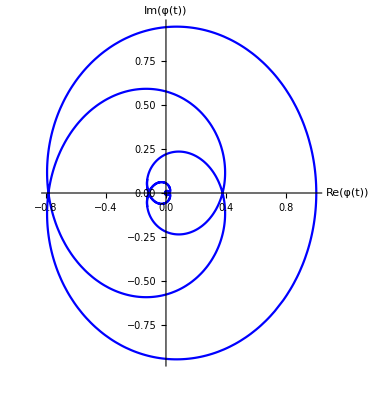

```mathematica
ParametricPlot[{Re[CharacteristicFunction[BinomialDistribution[10,2/3],t]],Im[CharacteristicFunction[BinomialDistribution[10,2/3],t]]},{t,-5,5},PlotRange->All,PlotStyle->Blue, AxesLabel->{Re[φ[t]],Im[φ[t]]}]
```

Teorema de inversión

La fórmula de inversión para el caso discreto que usa Mathematica es(|b/(2 π)|)^((a+1)/2)∫_(-π/(|b|))^(π/(|b|)) ϕ(t) ⅇ^(ⅈ b n t)ⅆω.
Es equivalente a la usada en probabilidad, con parámetros {1,-1} , solo es válida para distribuciones reticulares.

Mediante la Transformada inversa de Fourier.

Comando: InverseFourierSequenceTransform

Opciones: FourierParameters→{1,1}

```mathematica
InverseFourierSequenceTransform[(1-p+p ⅇ^(ⅈ t))^5,t,x,FourierParameters->{1,-1}]
```

Piecewise[{{(1-p)^(5-x) p^x Binomial[5,x], 0≤x≤5}, {0, True}}]

Mediante los coeficientes de la serie de Fourier.

```mathematica
FourierCoefficient[(1-p+p ⅇ^(ⅈ t))^5,t,x]
```

Piecewise[{{(1-p)^(5-x) p^x Binomial[5,x], 0≤x≤5}, {0, True}}]

Otras transformaciones

Función generatriz de probabilidad (de momentos factoriales): MomentFactorialGeneratingFunction

```mathematica
FactorialMomentGeneratingFunction[BinomialDistribution[n,p],t]
```

(1+p (-1+t))^n

Función generatriz: GeneratingFunction

```mathematica
GeneratingFunction[PDF[BinomialDistribution[n,p],x],x,t]
```

(1+p (-1+t))^n

Probabilidades a partir de las derivadas de la función generatriz de probabilidad

Comando: D

```mathematica
Table[D[FactorialMomentGeneratingFunction[BinomialDistribution[5,p],t],{t,x}]/Factorial[x] /.t->0,{x,0,5}]
```

{(1-p)^5,5 (1-p)^4 p,10 (1-p)^3 p^2,10 (1-p)^2 p^3,5 (1-p) p^4,p^5}